# Just launch the code below to run the notebook (shift+enter)

```mathematica
ClearAll["Global`*"]
ParallelEvaluate[ClearAll["Global`*"]];
BlockEvaluation[tag_]:=Block[{},
nb=EvaluationNotebook[];
NotebookFind[nb,tag,All,CellTags];
SelectionEvaluate[nb]
]
CloseKernels[];
LaunchKernels[];
dropdownDialog[list_,phrase_]:=DialogInput[{choice=""},Column[{TextCell[phrase],PopupMenu[Dynamic[choice],list],Button["OK",DialogReturn[choice]]}]]
infoDialog[phrase_]:=DialogInput[{choice=""},Column[{TextCell[phrase],Button["Proceed",DialogReturn[choice]]}]]
If[(DirectoryQ[FileNameJoin[{NotebookDirectory[],"Auxiliary data"}]]//ToString)=="False",CreateDirectory[FileNameJoin[{NotebookDirectory[],"Auxiliary data"}]]];
choiceslist={"Tabulated Nevents+sensitivity","Sensitivity only (tabulated Nevents must be produced before)","Acceptance"};
taglist["Acceptance"]="Acceptance";
taglist["Tabulated Nevents+sensitivity"]="Number-of-events+sensitivity";
taglist["Sensitivity only (tabulated Nevents must be produced before)"]="Sensitivity";
computationchoice=dropdownDialog[choiceslist,"Do you want to compute the tabulated number of events and then sensitivity, or just sensitivity (if the tabulated number of events has been already produced)?"];
tagselected=taglist[computationchoice]
BlockEvaluation[tagselected]
```

Number-of-events+sensitivity

# Definitions

## Various directories

```mathematica
LLPdirName="DP";
(*Set the directory for the search where tabulated acceptances are located*)
directory["Acceptances"]=FileNameJoin[{NotebookDirectory[],"Acceptances"}];
(*Set the directory for the search where tabulated angle-energy distributions are located*)
directory["Distribution"]=FileNameJoin[{NotebookDirectory[],"spectra/New physics particles spectra",LLPdirName}]; 
(*The directory storing production weights of the given LLP*)
directory["Production weights"]=FileNameJoin[{NotebookDirectory[],"phenomenology",LLPdirName,"Production probabilities"}]; 
(*Directory to which various auxillary datasets will be stored*)
directory["Auxiliary"]=FileNameJoin[{NotebookDirectory[],"Auxiliary data",LLPdirName}]; 
If[!DirectoryQ[directory["Auxiliary"]],CreateDirectory[directory["Auxiliary"]]];
(*Directory containing decay widths of the LLPs*)
directory["Decays"]=FileNameJoin[{NotebookDirectory[],"phenomenology",LLPdirName,"decay widths"}];
```

## Parameters and critical definitions

```mathematica
dropdownDialog[list_,phrase_]:=DialogInput[{choice=""},Column[{TextCell[phrase],PopupMenu[Dynamic[choice],list],Button["OK",DialogReturn[choice]]}]]
infoDialog[phrase_]:=DialogInput[{choice=""},Column[{TextCell[phrase],Button["Proceed",DialogReturn[choice]]}]]
selectionDialog[list_,phrase_]:=DialogInput[{choice={}},Column[{Row[{phrase}],Pane[TogglerBar[Dynamic[choice],list,Appearance->"Vertical"->{Automatic,5}],ImageSize->{Automatic,Automatic},Scrollbars->{False,True}],Button["OK",DialogReturn[choice]]}]]
(*Conversion units*)
GeVMinusOneTom=2*10^-16;
chbarval=3*10^8*6.58*10^-25;
(*EM coupling*)
αEM=1/137;
(*Mesons masses*)
{mSM["Rho0"],mSM["Pi0"],mSM["Eta"],mSM["EtaPr"],mSM["p"]}={0.775,0.135,0.547,0.958,0.939};
ΓSM["ρ780"]=0.149;
σpNucleonInpb[Atarget_]=51*Atarget^-0.29*10^9;
```

## LLP phenomenology: production probabilities, decay widths

## Scanning for tabulated distributions

```mathematica
(*Define the file pattern*)
pattern="DoubleDistr_*_*_*.m";
(*Search for files matching the pattern in the directory and its subdirectories*)
matchingFiles=FileNames[pattern,{directory["Distribution"]},Infinity];
(*List of LLPs, production modes, and facilities for which the tabulated distributions have been computed at the previous stage of using SensCalc*)
ExtractedProductionParameters=Function[filename,parts=StringSplit[FileNameTake[filename],"_"];
{parts[[2]],parts[[3]],StringDrop[parts[[4]],-2]} ];
(*combinations selected LLP, production channel, facility for which the tabulated distributions are present*)
DistrCombinations=(ExtractedProductionParameters/@matchingFiles)//Sort
```

(DP | Bremsstrahlung | LHC
DP | Bremsstrahlung | SPS
DP | DrellYan | FermilabBD
DP | DrellYan | LHC
DP | DrellYan | SPS
DP | Eta | LHC
DP | Eta | SPS
DP | EtaPr | LHC
DP | EtaPr | SPS
DP | Pi0 | LHC
DP | Pi0 | SPS
DP | Rho0 | LHC
DP | Rho0 | SPS)

## Production probabilities

### Via decays of mesons and mixing: br ratios and meson multiplicities

```mathematica
(*Production from decays of mesons and mixing with ρ^0*)
BrπToγγ=0.98799;
BrηToγγ=0.3931181;
(*BrωToπγ=0.0834941;*)
BrηprToγγ=0.0219297;
Brπ0ToV[mLLP_]=If[mLLP<mSM["Pi0"],Evaluate[2*(1-mLLP^2/mSM["Pi0"]^2)^3*BrπToγγ],0];
BrηToV[mLLP_]=If[mLLP<mSM["Eta"],Evaluate[2*(1-mLLP^2/mSM["Eta"]^2)^3*BrηToγγ],0];
(*BrωToV[mLLP_]=If[mLLP<mω-mπ0,BrωToπγ*(mω^2-mLLP^2-mπ0^2)^2*Sqrt[(mω^2-mLLP^2+mπ0^2)^2-4*mω^2*mπ0^2]/(mω^2-mLLP^2)^3,0];*)
BrηprToV[mLLP_]=If[mLLP<mSM["EtaPr"],Evaluate[2*(1-mLLP^2/mSM["EtaPr"]^2)^3*BrηprToγγ],0];
{BrDecay[mLLP_,ϵ2_,"Pi0"],BrDecay[mLLP_,ϵ2_,"Eta"],BrDecay[mLLP_,ϵ2_,"EtaPr"]}=ϵ2*{Brπ0ToV[mLLP],BrηToV[mLLP],BrηprToV[mLLP]};
(*Mixing angle ρ^0-DP. Following https://arxiv.org/pdf/1810.01879.pdf*)
gρ0=5;
θDPρ02[mLLP_,ϵ2_]=ϵ2*(4Pi*αEM)/gρ0^2 mSM["Rho0"]^4/((mLLP^2-mSM["Rho0"]^2)^2+ΓSM["ρ780"]^2*mSM["Rho0"]^2);
FacilitiesList={"SPS","FermilabBD","LHC","FCC-hh","Serpukhov"};
Do[
PmotherToLLP[mLLP_,ϵ2_,part,Facility]=BrDecay[mLLP,ϵ2,part];
,{part,{"Pi0","Eta","EtaPr"}},{Facility,FacilitiesList}]
Do[
PmotherToLLP[mLLP_,ϵ2_,"Rho0",Facility]=θDPρ02[mLLP,ϵ2];
,{Facility,FacilitiesList}]
(*________________*)
(*Bremsstrahlung*)
(*________________*)
bremfacilities=Select[DistrCombinations,#[[2]]=="Bremsstrahlung"&][[All,3]];
BremProd[Facility_]:=Module[{},
If[MemberQ[bremfacilities,Facility],
datbrem[mLLP_,θLLP_]=Import[FileNameJoin[{directory["Production weights"],"Pbrem_"<>LLPdirName<>"_"<>Facility<>".m"}],"MX"];
PmotherToLLP[mLLP_,ϵ2_,"Bremsstrahlung",Facility]=datbrem[mLLP,θLLP][[1]]*ϵ2;
ELLPmin["Bremsstrahlung",Facility]=Evaluate[datbrem[mLLP,θLLP][[2]]];
ELLPmax[mLLP_,θLLP_,"Bremsstrahlung",Facility]=Evaluate[datbrem[mLLP,θLLP][[3]]]
]
]
Do[
BremProd[Facility],{Facility,FacilitiesList}]
(*_____________________________*)
(*Production from Drell-Yan process*)
(*_____________________________*)
(*Average enhancement LO vs LO+NLO obtained for SPS energies in 2011.05115*)
kfactorNLO=1.7;
σDrellYanData[Facility_]:=Block[{},
dat=Import[FileNameJoin[{directory["Production weights"],"sigmaDrellYan_DP_"<>Facility<>".txt"}],"Table"];
MinMaxMassesDrellYan[Facility]={Min[dat[[All,1]]],Max[dat[[All,1]]]};
int[ma_]=If[MinMaxMassesDrellYan[Facility][[1]]≤ ma≤MinMaxMassesDrellYan[Facility][[2]],Evaluate[10^(Interpolation[{Log10[#[[1]]],Log10[#[[2]]+10^-90]}&/@dat,InterpolationOrder->1][Log10[ma]])],0];
PmotherToLLP[mLLP_,ϵ2_,"DrellYan",Facility]=If[Facility=="SPS",kfactorNLO,1]*ϵ2*int[mLLP]/σpNucleonInpb[Atarget]
]
Do[σDrellYanData[Facility],{Facility,{"SPS","FermilabBD","LHC"}}]
WeightsCombinations=Cases[Keys[DownValues@PmotherToLLP][[All,1,#]]&/@{3,4}//Transpose//Sort,_?(MemberQ[DistrCombinations[[All,{2,3}]],#]&)];
Print["If there are production weights to all available distributions:"]
IfCondDistrToWeights=DistrCombinations[[All,{2,3}]]==WeightsCombinations
If[!IfCondDistrToWeights,infoDialog["You have not provided the production probabilities PmotherToLLP to all the generated tabulated distributions! Please do this first to avoid problems"];]
```

If there are production weights to all available distributions:

True

## Decays

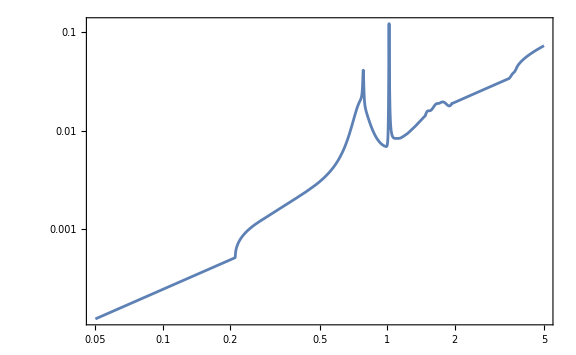

```mathematica
(*Decay width in GeV*)
ΓLLP[mLLP_,ϵ2_]=ϵ2*10^(Interpolation[{Log10[#[[1]]],Log10[#[[2]]]}&/@Import[FileNameJoin[{directory["Decays"],"GammaDarkPhoton.txt"}],"Table"],InterpolationOrder->1][Log10[mLLP]]);
LogLogPlot[ΓLLP[mLLP,1],{mLLP,0.05,5},Frame->True,ImageSize->Large]
(*Decay length*)
cτLLP[mLLP_,ϵ2_]=chbarval/ΓLLP[mLLP,ϵ2];
ldecayLLP[mLLP_,ϵ2_,ELLP_]=cτLLP[mLLP,ϵ2]*(√(ELLP^2-mLLP^2))/mLLP;
```

## Loading necessary routines

```mathematica
If[Length[inecessary]==0,
NotebookEvaluate[FileNameJoin[{NotebookDirectory[],"codes/generic.nb"}]];
NotebookEvaluate[FileNameJoin[{NotebookDirectory[],"codes/for-sensitivities.nb"}]];
inecessary={1,2,3};
]
```

# Specifying the experiment and run next sections

## Specifying the experiment

```mathematica
SetDirectory[NotebookDirectory[]];
(*Parent directory*)
NotebookDirectory[]//ParentDirectory;
ExperimentDirectoriesList=Select[FileNames["*",directory["Acceptances"],1],DirectoryQ];
(*List of available experiments (for which the geometry has been implemented)*)
ExperimentsListTemp=Table[FileNameTake[ExperimentDirectoriesList[[i]],-1],{i,1,Length[ExperimentDirectoriesList],1}];
ExperimentsListTemp2=Join[Partition[ExperimentsListTemp,1],Table[{TrueQ@FileExistsQ@FileNameJoin[{directory["Acceptances"],ExperimentsListTemp[[i]],ToString@StringForm["Acceptance_``_for_``.m",Sequence@@{ExperimentsListTemp[[i]],LLPdirName}]}]},{i,1,Length[ExperimentsListTemp]}],2];
ExperimentsList=Select[ExperimentsListTemp2,#[[2]]==True&][[All,1]]//Sort
If[Length[ExperimentsList]==0,Print["No experiment is available, generate first the acceptance for the given experiment using module 1"]]
Print["Selected experiments:"]
SelectedExperimentList=If[Length[ExperimentsList]≠0,selectionDialog[ExperimentsList,"Select the experiments:"]]
icounter=1;
```

{SHiP-ECN4}

Selected experiments:

{SHiP-ECN4}

## Running block for next sections

```mathematica
BlockEvaluation[tag_]:=Block[{},
nb=EvaluationNotebook[];
NotebookFind[nb,tag,All,CellTags];
SelectionEvaluate[nb]
]
If[tagselected=="Number-of-events+sensitivity",
Do[
BlockEvaluation["Number-of-events-computation+sensitivity"];
,{icounter,1,Length[SelectedExperimentList],1}],
If[tagselected=="Acceptance",
Do[
BlockEvaluation["Acceptance-computation"];
,{icounter,1,Length[SelectedExperimentList],1}]
]
]
```

# Number of events

## Particular experiment

```mathematica
SelectedExperiment=SelectedExperimentList[[icounter++]];
```

## Cross-sections, acceptances

{0.411314,Null}

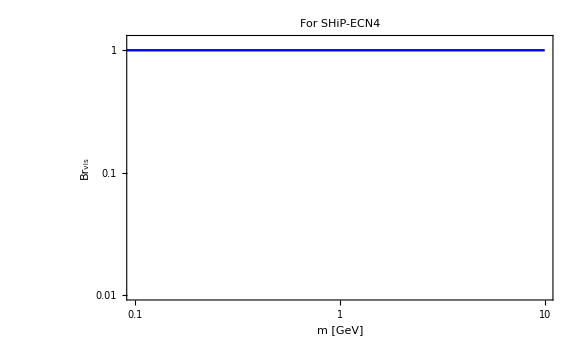

Search for DP at SHiP-ECN4 located at SPS. N_collisions = 6.×10^20

Quantity | θ_min, rad | θ_max, rad | θ_min(ϵ_dec), rad | θ_max(ϵ_dec), rad | z_min, m | z_max, m
Description | Min angle covered by experiment | Max angle covered by experiment | Min angle where ϵ_decay≠0 | Max angle where ϵ_decay≠0 | Min long. displacement of the decay volume | Max long. displacement of the decay volume
Value | 0.00001 | 0.0602815 | 0.00001 | 0.0602815 | 50. | 100.

```mathematica
dataAcceptances=Import[FileNameJoin[{FileNameJoin[{directory["Acceptances"],SelectedExperiment,ToString@StringForm["Acceptance_``_for_``.m",Sequence@@{SelectedExperiment,LLPdirName}]}]}],"MX"];//AbsoluteTiming
{FacilityGivenExperiment,FullAcceptanceData0,BrVis[mLLP_]}=dataAcceptances[[#]]&/@{1,3,5};
LogLogPlot[Evaluate[BrVis[mLLP]],{mLLP,0.02,10},Frame->True,ImageSize->Large,FrameStyle->Directive[Black, 22],PlotStyle->{{Thickness[0.003],Blue},{Thickness[0.003],Darker@Red},{Thickness[0.003],Darker@Darker@Green},{Thickness[0.003],Black}},GridLines->Automatic,PlotRange->{{0.1,10},{0.01,1.2}},Frame->True,ImageSize->Large,FrameLabel->{"m [GeV]","Br_vis"},PlotLabel-> Style[Row[{"For ",SelectedExperiment}], 20, Black]]
(*___________________________*)
(*Interpolation of the tabulated azimuthal acceptance, extracting Subscript[θ, min/max], etc.*)
(*___________________________*)
{AzimuthalAcceptanceInt[θLLP_,zLLP_],θminExpAll,θmaxExpAll,θminExp,θmaxExp,zminExp,zmaxExp,zminθ[θLLP_],zmaxθ[θLLP_]}=BlockϵAzimuthal[FullAcceptanceData0];
(*Logarithmized data with full acceptance, and also decay acceptance and full acceptance interpolations*)
{FullAcceptanceData,DecayAcceptanceInt[mLLP_,θLLP_,ELLP_,zLLP_],FullAcceptanceInt[mLLP_,θLLP_,ELLP_,zLLP_],InGridmϵ,InGridθϵ,InGridEϵ,InGridzϵ,ϵvals,ϵazvals,mminϵ,mmaxϵ}=BlockϵDecay[FullAcceptanceData0,zminExp,BrVis];
CrossSectionData=dataAcceptances[[4]]//Transpose;
listquantities=((#//ToString)&/@{Npot,PPi0,PEta,PEtapr,PRho0,Atarget});
quantityselector[quantity_]:=Select[CrossSectionData,#[[1]]==quantity&][[1]][[2]]//N;
{NpotGivenExperiment,ProbMother["Pi0"],ProbMother["Eta"],ProbMother["EtaPr"],ProbMother["Rho0"],AtargetVal}=Table[quantityselector[quantity],{quantity,listquantities}];
ProbMother["DrellYan"]=ProbMother["Bremsstrahlung"]=1.;
(*infoDialog[Row[{"The number of proton collisions is ", NpotGivenExperiment,". You may change it at the stage of computing the sensitivities"}]]*)
Row[{"Search for "<>LLPdirName<>" at ", SelectedExperiment, " located at ",FacilityGivenExperiment,". N_collisions = ",NpotGivenExperiment}]
{{"Quantity","θ_min, rad","θ_max, rad","θ_min(ϵ_dec), rad","θ_max(ϵ_dec), rad","z_min, m","z_max, m"},{"Description","Min angle covered by experiment","Max angle covered by experiment","Min angle where ϵ_decay≠0","Max angle where ϵ_decay≠0","Min long. displacement of the decay volume","Max long. displacement of the decay volume"},{"Value",θminExpAll,θmaxExpAll,θminExp,θmaxExp,zminExp,zmaxExp}}//TableForm
```

## Angle-energy distributions and differential yields for the given experiment

Production list:

{Bremsstrahlung,DrellYan,Eta,EtaPr,Pi0,Rho0}

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{0.209556,Null}

{3.44644,Null}

InterpolatingFunction::dmval: Input value {0.1,-4.99992} lies outside the range of data in the interpolating function. Extrapolation will be used.

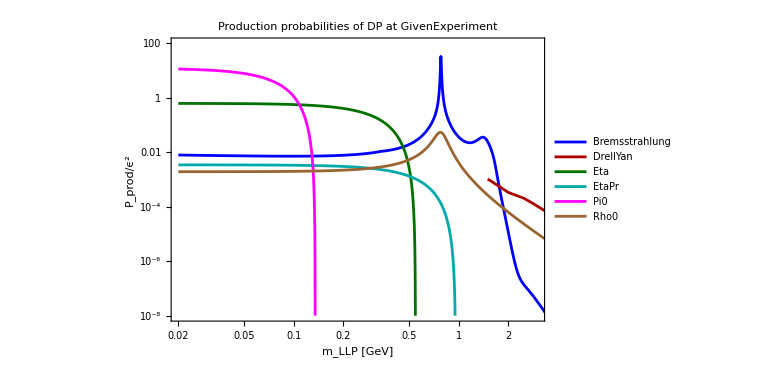
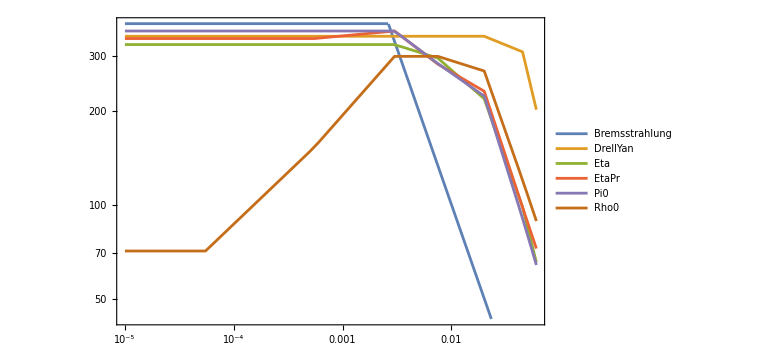

```mathematica
ProductionPatternSelected=Select[DistrCombinations,#[[3]]==FacilityGivenExperiment&];
Print["Production list:"]
ELLPmax[mLLP_,θLLP_,"Bremsstrahlung"]=ELLPmax[mLLP,θLLP,"Bremsstrahlung",FacilityGivenExperiment];
ELLPmin["Bremsstrahlung"]=ELLPmin["Bremsstrahlung",FacilityGivenExperiment];
ProductionListTemp=ProductionPatternSelected[[All,2]]//DeleteDuplicates;
ProductionList=If[ELLPmin["Bremsstrahlung"]<ELLPmax[0.02,θminExp,"Bremsstrahlung"],ProductionListTemp,Select[ProductionListTemp,#!="Bremsstrahlung"&]]
θmaxBrem=Abs[θLLP/.Solve[ELLPmax[0.02,θLLP,"Bremsstrahlung"][[2]]==ELLPmin["Bremsstrahlung"],θLLP][[1]]];
Do[
Module[{prod},
prod=ProductionPatternSelected[[i]][[2]];
(*Importing the data with distribution*)
dirimp=If[prod=="DrellYan",FileNameJoin[{directory["Distribution"],"Pregenerated"}],directory["Distribution"]];
DistrDataImport[prod]=Import[FileNameJoin[{dirimp,"DoubleDistr_"<>LLPdirName<>"_"<>prod<>"_"<>FacilityGivenExperiment<>".m"}],"MX"];
If[prod=="DrellYan",
DistrDataImport[prod]=Select[DistrDataImport[prod],MinMaxMassesDrellYan[FacilityGivenExperiment][[1]]<=#[[1]]<=MinMaxMassesDrellYan[FacilityGivenExperiment][[2]]&];
];
(*Min/mass mass of the LLP from the data*)
mlistDistr[prod]=DeleteDuplicates[DistrDataImport[prod][[All,1]]];
{mLLPmin[prod],mLLPmax[prod]}=MinMax[mlistDistr[prod]];
(*Interpolation of the tabulated distribution*)
DoubleDistrLLPint[mLLP_,θLLP_,ELLP_,prod]=10^(Interpolation[distrlogComp[DistrDataImport[prod]],InterpolationOrder->1][Log10[mLLP],Log10[θLLP],Log10[ELLP]]);
If[prod=="Bremsstrahlung",
DoubleDistrLLPint[mLLP_,θLLP_,ELLP_,prod]=If[ELLP<=ELLPmax[mLLP,θLLP,"Bremsstrahlung"],Evaluate[DoubleDistrLLPint[mLLP,θLLP,ELLP,prod]],0.]];
(*Probability to produce LLP*)
ProbLLP[mLLP_,finv_,prod]=ProbMother[prod]*PmotherToLLP[mLLP,finv,prod,FacilityGivenExperiment]/.{Atarget->AtargetVal};
]
,{i,1,Length[ProductionPatternSelected],1}]
directory["Auxiliary-experiment"]=FileNameJoin[{directory["Auxiliary"],SelectedExperiment}];
If[!DirectoryQ[directory["Auxiliary-experiment"]],CreateDirectory[directory["Auxiliary-experiment"]]];
Export[FileNameJoin[{directory["Auxiliary-experiment"],"Double-Distr-Averaged-"<>LLPdirName<>".m"}],{Sum[If[mLLPmin[prod]<mLLP<mLLPmax[prod],Evaluate[ProbLLP[mLLP,1,prod]],0],{prod,ProductionList}],1/Sum[If[mLLPmin[prod]<mLLP<mLLPmax[prod],Evaluate[ProbLLP[mLLP,1,prod]],0],{prod,ProductionList}] Sum[If[mLLPmin[prod]<mLLP<mLLPmax[prod],Evaluate[ProbLLP[mLLP,1,prod]*DoubleDistrLLPint[mLLP,θLLP,ELLP,prod]],0],{prod,ProductionList}]},"MX"];
Do[{GridInFinal[prod],DistrVals[prod]}=BlockGridsValsDistr[prod,DistrDataImport],{prod,ProductionList}];//AbsoluteTiming
(*____________________________*)
(*Finding Subscript[E, max](Subscript[m, LLP],Subscript[θ, LLP]) for the angular range at the given experiment*)
(*____________________________*)
Do[ELLPmax[mfip_,θfip_,prod]=EmaxBlock[prod,8,DistrDataImport,FacilityGivenExperiment],{prod,Select[ProductionList,#!="Bremsstrahlung"&]}]//AbsoluteTiming
ptenergies=LogLogPlot[Evaluate[Table[ELLPmax[0.1,θLLP,prod],{prod,ProductionList}]],{θLLP,θminExp,θmaxExp},Frame->True,ImageSize->Large,PlotLegends->Placed[Style[#,15]&/@ProductionList,Right]];
ptprodprob=LogLogPlot[Evaluate[Table[ProbLLP[ma,1,prod],{prod,ProductionList}]],{ma,mminϵ,mmaxϵ},Frame->True,ImageSize->Large,PlotLegends->Placed[Style[#,16]&/@ProductionList,{0.2,0.28}], FrameStyle->Directive[Black, 25],PlotRange->{{0.02,3},{10^-8,100}},PlotStyle->{{Thick,Blue},{Thick,Darker@Red},{Thick,Darker@Darker@Green},{Thick,Darker@Cyan},{Thick,Magenta},{Thick,Brown}},AspectRatio->0.66,ImageSize->Large,FrameLabel->{"m_LLP [GeV]","P_prod/ϵ^2"},PlotLabel->Style[Row[{"Production probabilities of ",LLPdirName," at ",GivenExperiment}],18,Black]];
Style[Row[{ptprodprob,ptenergies}],ImageSizeMultipliers->{1, 1}]
```

## Number of events

## Number of events - using the mapping method

### Initializing all routines

```mathematica
Do[{OutGridθfinal[prod],Δθvals[prod]}=OutGridθTemp[InGridθϵ,30,prod,θmaxBrem],{prod,ProductionList}]
{OutGridzfinal,Δzvals}=OutGridszTemp[InGridzϵ,30,zminExp];
(*Final energy grid. Mass- and production channel-dependent*)
If[FacilityGivenExperiment!="ESS",
StepEtemp[Efip_]=Piecewise[{{0.3,Efip≤2.5},{0.5,2.5<Efip<35},{2,35≤Efip≤50},{4,50<Efip<160},{5,160≤Efip<=400},{25,400<Efip<600},{50,600<=Efip<2000},{200,2000≤Efip<4000},{400,4000≤Efip<7000},{500,7000≤Efip≤50000}}];
OutGridEnergy[m_,ProdChannel_]:=Block[{},
emin=If[ProdChannel!="Bremsstrahlung",N[m],ELLPmin["Bremsstrahlung"]];
egridtemp=With[{start=emin,end=ELLPmax[m,θminExp,ProdChannel]},
Log10[NestWhileList[#+StepEtemp[#]&,start,#≤end&,1,∞,-1]]]//N;
If[Length[egridtemp]==1,egridtemp=Join[egridtemp,{Log10[2*emin]}]];
egridtemp
]
,
StepEtemp[Efip_]=0.001;
OutGridEnergy[m_,ProdChannel_]:=Block[{},
tabt=Table[e,{e,1.0001m,ELLPmax[m,θminExp,ProdChannel],0.001}];
If[Length[tabt]==1,tabt=Join[tabt,{ELLPmax[m,θminExp,ProdChannel]}]//Sort//DeleteDuplicates];
Log10[tabt]//N
]
]
(*____________________________________________________*)
(*Block that computes the grid Subscript[θ, S],Subscript[E, S],Subscript[z, S], Subscript[ϵ, Full]×Subscript[f, Subscript[θ, S],Subscript[E, S]]*)
(*____________________________________________________*)
(*The block which sets all the values of Subscript[ϵ, Full]×Subscript[f, θ,E] for which E < Subscript[E, max] to zero, for Bremsstrahlung*)
emaxbrem[mLLP_,θLLP_]=ELLPmax[mLLP,θLLP,"Bremsstrahlung"];
BremCutComp=Hold@Compile[{{angleenergy,_Real,1},{mfip,_Real}},Module[{angles,energies,distrvals,d},
angles=Compile`GetElement[angleenergy,1];
energies=Compile`GetElement[angleenergy,2];
distrvals=Compile`GetElement[angleenergy,3];
d=If[energies<emaxbrem[mfip,angles],distrvals,10^-90.];
d
],CompilationTarget->"C",RuntimeOptions->"Speed",RuntimeAttributes->{Listable}]/.DownValues@emaxbrem//ReleaseHold;
BremCut[OutGridθfinal_,OutGridEfinal_,distr_,mLLP_]:=Block[{},
angleenergy=Join[10^Tuples[{OutGridθfinal,OutGridEfinal}],Partition[distr,1],2];
BremCutComp[angleenergy,mLLP]
]
TableIntegrandDiscret[m_,ProdChannel_,ϵDecOp_]:=TableIntegrandDiscretTemp[m,ProdChannel,ϵDecOp,ϵvals,ϵazvals,OutGridθfinal[ProdChannel],OutGridzfinal,OutGridEnergy,InGridmϵ,InGridθϵ,InGridEϵ,InGridzϵ,Δθvals[ProdChannel],Δzvals,zminExp,GridInFinal,DistrVals,FacilityGivenExperiment]
```

### Generalized acceptances

{16.4264,Null}

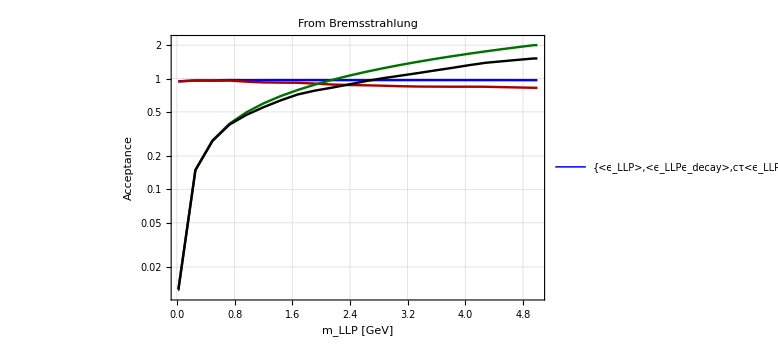
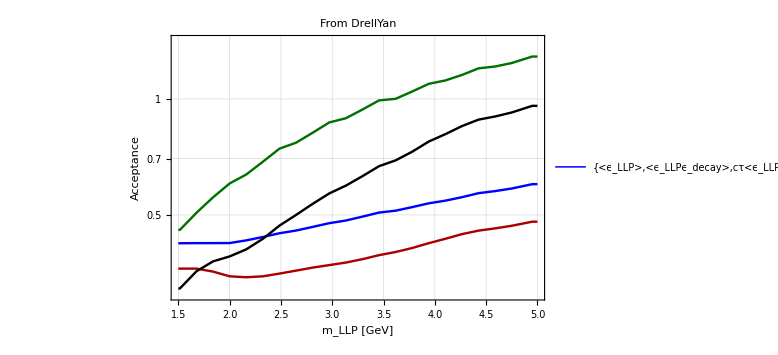
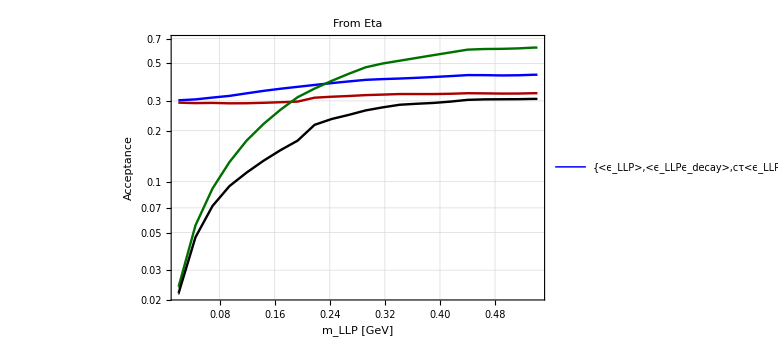
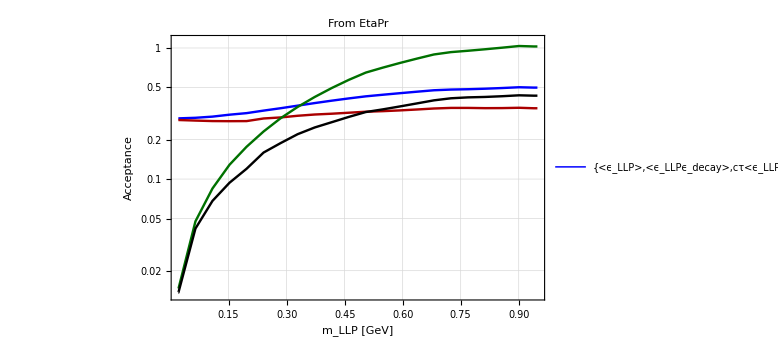
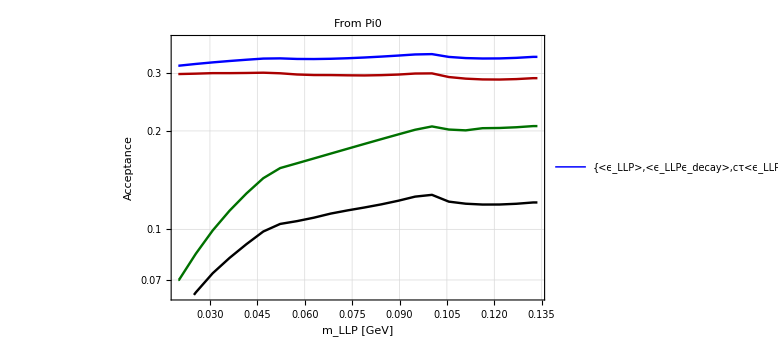
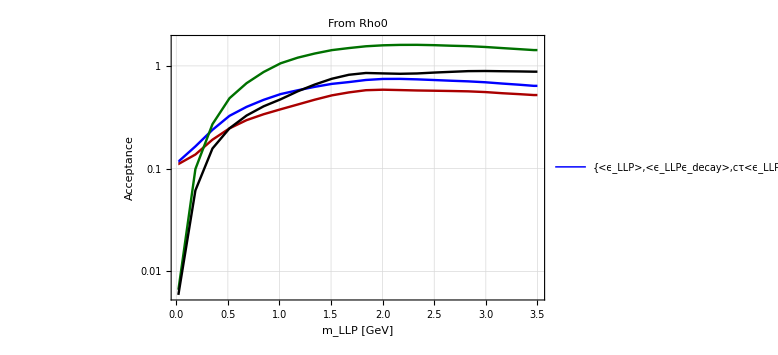

```mathematica
(*Tabulated acceptance*)
FactorANUBISceiling=If[SelectedExperiment=="ANUBIS-ceiling",2,1];
AcceptanceDiscret[m_,ProdChannel_,ϵdecOp_,decProb_]:=AcceptanceDiscretTemp[m,ProdChannel,ϵdecOp,decProb,mLLPmin,mminϵ,mLLPmax,mmaxϵ,ELLPmax,θminExp,TableIntegrandDiscret,BrVis,zmaxExp,zminExp,FactorANUBISceiling,0.]
Do[mlistAcceptance[prod]=Join[Table[m,{m,1.01Max[mLLPmin[prod],mminϵ],0.95Min[mLLPmax[prod],mmaxϵ],Min[(0.95Min[mLLPmax[prod],mmaxϵ]-1.01Max[mLLPmin[prod],mminϵ])/20,2]}],{0.99Min[mLLPmax[prod],mmaxϵ]}],{prod,ProductionList}];
Do[
ϵGeomTabs[prod]=ParallelTable[{m,AcceptanceDiscret[m,prod,"False",0],AcceptanceDiscret[m,prod,"True",0],AcceptanceDiscret[m,prod,"False",1],AcceptanceDiscret[m,prod,"True",1]},{m,mlistAcceptance[prod]}];
ϵGeomTabs[prod]=Join[{Join[{Max[mLLPmin[prod],mminϵ]},Drop[ϵGeomTabs[prod][[1]],1]]},ϵGeomTabs[prod],{Join[{Min[mLLPmax[prod],mmaxϵ]},Drop[ϵGeomTabs[prod][[-1]],1]]}];
,{prod,ProductionList}];//AbsoluteTiming
PlotAcc[ProdChannel_]:=ListLogPlot[Evaluate[{ϵGeomTabs[ProdChannel][[All,{1,2}]],ϵGeomTabs[ProdChannel][[All,{1,3}]],ϵGeomTabs[ProdChannel][[All,{1,4}]],ϵGeomTabs[ProdChannel][[All,{1,5}]]}],FrameStyle->Directive[Black, 22],PlotStyle->{{Thickness[0.003],Blue},{Thickness[0.003],Darker@Red},{Thickness[0.003],Darker@Darker@Green},{Thickness[0.003],Black}},GridLines->Automatic,PlotRange->{MinMax[ϵGeomTabs[ProdChannel][[All,1]]],{Max[0.9Min[Min[ϵGeomTabs[ProdChannel][[All,4]]],Min[ϵGeomTabs[ProdChannel][[All,3]]]],10^-5],1.1Max[Max[ϵGeomTabs[ProdChannel][[All,2]]],Max[ϵGeomTabs[ProdChannel][[All,4]]]]}},Joined->True,Frame->True,ImageSize->Large,FrameLabel->{"m_LLP [GeV]","Acceptance"},PlotLabel-> Style[Row[{"From ",ProdChannel}], 20, Black],PlotLegends->Placed[{Style[#, 18]&/@{"<ϵ_LLP>","<ϵ_LLPϵ_decay>","cτ<ϵ_LLPP_decay>","cτ<ϵ_LLPP_decayϵ_decay>"}},{0.75,0.2}]]
Style[Row[Evaluate[Table[PlotAcc[prod],{prod,ProductionList}]]],ImageSizeMultipliers->{1,1,1,1}]
(*Do[FilenameAcceptance[prod]=ToString@StringForm["Acceptance_ALP-fermion_at_``_From_``.dat",Sequence@@{SelectedExperiment,ExportList[prod]}];
Export[FileNameJoin[{NotebookDirectory[],"Auxiliary data/ALPs with fermion coupling",SelectedExperiment,FilenameAcceptance[prod]}],ϵGeomTabs[prod][[All,{1,2,4,5}]],"Table"]
,{prod,ProductionList}]*)
AccAveraged[mLLP_,cτ_]=NpotGivenExperiment{Sum[If[mLLPmin[prod]<mLLP<mLLPmax[prod],Evaluate[ProbLLP[mLLP,1,prod]],0],{prod,ProductionList}],Sum[If[Max[mLLPmin[prod],mminϵ]<mLLP<Min[mLLPmax[prod],mmaxϵ],Evaluate[ProbLLP[mLLP,1,prod]*Interpolation[ϵGeomTabs[prod][[All,{1,2}]],InterpolationOrder->1][mLLP]],0],{prod,ProductionList}],Sum[If[Max[mLLPmin[prod],mminϵ]<mLLP<Min[mLLPmax[prod],mmaxϵ],Evaluate[ProbLLP[mLLP,1,prod]/cτ*Interpolation[ϵGeomTabs[prod][[All,{1,4}]],InterpolationOrder->1][mLLP]],0],{prod,ProductionList}],Sum[If[Max[mLLPmin[prod],mminϵ]<mLLP<Min[mLLPmax[prod],mmaxϵ],Evaluate[ProbLLP[mLLP,1,prod]/cτ*Interpolation[ϵGeomTabs[prod][[All,{1,5}]],InterpolationOrder->1][mLLP]],0],{prod,ProductionList}]};
Export[FileNameJoin[{directory["Auxiliary-experiment"],"AcceptanceAveraged-"<>LLPdirName<>".m"}],AccAveraged[mLLP,cτ],"MX"];
```

### Rough estimates of the upper and lower bounds

InterpolatingFunction::dmval: Input value {0.5,-5.} lies outside the range of data in the interpolating function. Extrapolation will be used.

Bremsstrahlung

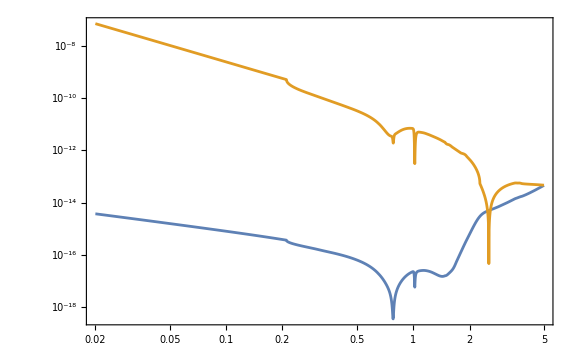

```mathematica
Do[LowerBoundEstimate[mLLP_,prod]=((NpotGivenExperiment*ProbLLP[mLLP,1,prod]*Interpolation[ϵGeomTabs[prod][[All,{1,5}]],InterpolationOrder->1][mLLP])/(2.3ldecayLLP[mLLP,1,ELLP] mLLP/(√(ELLP^2-mLLP^2))))^(-1/2);
UpperBoundEstimate[mLLP_,prod]=(Abs[Re[Evaluate[-ProductLog[-1,-2.3*b/a]/b/.{a-> NpotGivenExperiment*ProbLLP[mLLP,1,prod]*Interpolation[ϵGeomTabs[prod][[All,{1,3}]],InterpolationOrder->1][mLLP],b->zminExp/ldecayLLP[mLLP,1,ELLPmax[0.5,θminExp,prod]]}]]]),{prod,ProductionList}]
ProdTest=ProductionList[[1]]
LogLogPlot[Evaluate[{0.3LowerBoundEstimate[mLLP,ProdTest],1.8UpperBoundEstimate[mLLP,ProdTest]}],{mLLP,Max[mLLPmin[ProdTest],mminϵ],Min[mLLPmax[ProdTest],mmaxϵ]},Frame->True,ImageSize->Large]
```

### Number of events - fast

```mathematica
FactorLowerBound=If[MemberQ[{"ANUBIS-shaft-volume-1","ANUBIS-shaft-volume-2","ANUBIS-shaft-volume-3"},SelectedExperiment]==True,0.1,0.3];
NeventsDiscret[m_,ProdChannel_,couplinglist_]:=Module[{NevDiscret,NpotTimesχval,zshift},
If[Max[mLLPmin[ProdChannel],mminϵ]<m<Min[mLLPmax[ProdChannel],mmaxϵ],
integrandtab=TableIntegrandDiscret[m,ProdChannel,"True"];
NpotTimesχval[coupling_]=NpotGivenExperiment*ProbLLP[m,coupling,ProdChannel];
{lowerbound,upperbound}={LowerBoundEstimate[m,ProdChannel],UpperBoundEstimate[m,ProdChannel]};
brvis=BrVis[m];
NevDiscret[coupling_]:=If[0.1lowerbound<coupling<(*1.5*)2upperbound,NpotTimesχval[coupling]*brvis*sumcompile[tableprefac[integrandtab,m,cτLLP[m,coupling],1,0.]],0.];
Table[{m,couplinglist[[i]],NevDiscret[couplinglist[[i]]]},{i,1,Length[couplinglist],1}],Table[{m,couplinglist[[i]],0.},{i,1,Length[couplinglist],1}]]
]
```

### Number of events - slow (using built-in Mathematica functions Interpolation, NIntegrate)

```mathematica
(*Differential decay probability 1/ldecay Exp[-l/ldecay], where l is expressed in terms of the longitudinal displacement z and polar angle θ as z/cosθ*)
(*Differential decay probability (1/ldecay)Exp[-l/ldecay], where l is expressed in terms of the longitudinal displacement z and polar angle θ as z/cosθ*)
PdecayDensity[mLLP_,coupling_,θLLP_,ELLP_,zLLP_]=Exp[-zLLP/(Cos[θLLP]*ldecayLLP[mLLP,coupling,ELLP])]/(Abs[Cos[θLLP]]*ldecayLLP[mLLP,coupling,ELLP]);
(*The integrand determining the differential rate for events*)
Do[IntegrandLLP[mLLP_,coupling_,θLLP_,ELLP_,zLLP_,prod]=DoubleDistrLLPint[mLLP,θLLP,ELLP,prod]*PdecayDensity[mLLP,coupling,θLLP,ELLP,zLLP]*AzimuthalAcceptanceInt[θLLP,zLLP]*DecayAcceptanceInt[mLLP,θLLP,ELLP,zLLP],{prod,ProductionList}]
IntegralLLP[mLLP_,coupling_,ProdChannel_]:=NIntegrate[Abs[IntegrandLLP[mLLP,coupling,θLLP,Exp[ELLP],zLLP,ProdChannel]Exp[ELLP]],{θLLP,θminExp,θmaxExp},{ELLP,Log[mLLP],Log[ELLPmax[mLLP,θLLP,ProdChannel]]},{zLLP,zminθ[θLLP],zmaxθ[θLLP]},Method->"AdaptiveMonteCarlo"]
NeventsInt[mLLP_,coupling_,ProdChannel_]:=If[mLLPmin[ProdChannel]≤mLLP≤mLLPmax[ProdChannel]&&BrVis[mLLP]!=0,If[0.1LowerBoundEstimate[mLLP,ProdChannel]<coupling<2UpperBoundEstimate[mLLP,ProdChannel],NpotGivenExperiment*ProbLLP[mLLP,coupling,ProdChannel]*IntegralLLP[mLLP,coupling,ProdChannel],0.],0.]
IntegralLLPE[mLLP_,coupling_,ProdChannel_,ELLP_]:=NIntegrate[Abs[IntegrandLLP[mLLP,coupling,θLLP,ELLP,zLLP,ProdChannel]],{θLLP,θminExp,θmaxExp},{zLLP,zminθ[θLLP],zmaxθ[θLLP]},Method->"AdaptiveMonteCarlo"]
NeventsDiffInt[mLLP_,coupling_,ProdChannel_,ELLP_]:=If[mLLPmin[ProdChannel]≤mLLP≤mLLPmax[ProdChannel]&&BrVis[mLLP]!=0&&mLLP<ELLP<=ELLPmax[mLLP,θminExp,ProdChannel],If[0.1LowerBoundEstimate[mLLP,ProdChannel]<coupling<2UpperBoundEstimate[mLLP,ProdChannel],NpotGivenExperiment*ProbLLP[mLLP,coupling,ProdChannel]*IntegralLLPE[mLLP,coupling,ProdChannel,ELLP],0.],0.]
```

## Tests

#### Total number of events

```mathematica
(*This is a comparison between the slow and fast integration methods. For the selected mass and production channel, the numbers of events obtained using the methods should agree within 10%*)
(*If the agreement is worse, there may be a few reasons*)
(*1) The grid for the fast method is not dense enough. Try to increase the grid density (OutGridθfinal, OutGridEfinal, OutGridzfinal) to see whether the agreement improves. Sometimes, even a slightly denser grid for e.g. z may lead to a significant improvement in the agrement*)
(*2) The Monte-Carlo integrator for the slow method fails to evaluate properly; this may happen if the range of the integration over energies is too large compared to the domain where most of the events actually are (off-axis experiments such as MATHUSLA and ANUBIS). Another symptom is that for the given mass and coupling the integral "jumps", i.e., returns values with large error*)
(*A separate discussion should be made for the couplings belong to the domain cτ γ << Subscript[z, experiment]. The discrepancy may be significant, and the reason is insufficient grid density for the fast integration method. However, due to the exponential suppression of the number of events, this may be compensated by a tiny shift in the coupling, so the discrepancy should be considered as appropriate.*)
ProdTest=ProductionList[[2]];
mtest=Max[(mLLPmax[ProdTest]+mLLPmin[ProdTest])/2,1.2*mminϵ];
ϵ2list=(*{10^-12,3*10^-12,5*10^-12,10^-11,5*10^-11,10^-10,5*10^-10,10^-9,5*10^-9,10^-8,2*10^-8,4*10^-8,10^-7,5*10^-7,6*10^-7,7*10^-7,8*10^-7,9*10^-7,10^-6,2*10^-6}//N*)Table[10^x,{x,-17.,-3.,0.3}];
dat1=NeventsDiscret[mtest,ProdTest,ϵ2list];//AbsoluteTiming
dat2=ParallelTable[{ϵ2list[[i]],cτLLP[mtest,ϵ2list[[i]]],Quiet[NeventsInt[mtest,ϵ2list[[i]],ProdTest]]},{i,1,Length[ϵ2list],1}];//AbsoluteTiming
Join[{{"m_LLP/GeV","coupling","cτ/z_min","N_(events, fast)","N_(events, slow)"}},Join[dat1[[All,{1,2}]],{(#[[2]])/zminExp}&/@dat2,dat1[[All,{3}]],dat2[[All,{3}]],2]]//TableForm
```

{0.000088,Null}

{9.77257,Null}

m_LLP/GeV | coupling | cτ/z_min | N_(events, fast) | N_(events, slow)
5.75 | 1.×10^-17 | 4.57797 | 0. | 0.
5.75 | 1.99526×10^-17 | 2.29442 | 0. | 0.
5.75 | 3.98107×10^-17 | 1.14993 | 0. | 0.
5.75 | 7.94328×10^-17 | 0.576333 | 0. | 0.
5.75 | 1.58489×10^-16 | 0.28885 | 0. | 0.0276639
5.75 | 3.16228×10^-16 | 0.144768 | 0. | 0.0859154
5.75 | 6.30957×10^-16 | 0.072556 | 0. | 0.214866
5.75 | 1.25893×10^-15 | 0.0363641 | 0. | 0.403806
5.75 | 2.51189×10^-15 | 0.0182252 | 0. | 0.425964
5.75 | 5.01187×10^-15 | 0.00913425 | 0. | 0.
5.75 | 1.×10^-14 | 0.00457797 | 0. | 0.
5.75 | 1.99526×10^-14 | 0.00229442 | 0. | 0.
5.75 | 3.98107×10^-14 | 0.00114993 | 0. | 0.
5.75 | 7.94328×10^-14 | 0.000576333 | 0. | 0.
5.75 | 1.58489×10^-13 | 0.00028885 | 0. | 0.
5.75 | 3.16228×10^-13 | 0.000144768 | 0. | 0.
5.75 | 6.30957×10^-13 | 0.000072556 | 0. | 0.
5.75 | 1.25893×10^-12 | 0.0000363641 | 0. | 0.
5.75 | 2.51189×10^-12 | 0.0000182252 | 0. | 0.
5.75 | 5.01187×10^-12 | 9.13425×10^-6 | 0. | 0.
5.75 | 1.×10^-11 | 4.57797×10^-6 | 0. | 0.
5.75 | 1.99526×10^-11 | 2.29442×10^-6 | 0. | 0.
5.75 | 3.98107×10^-11 | 1.14993×10^-6 | 0. | 0.
5.75 | 7.94328×10^-11 | 5.76333×10^-7 | 0. | 0.
5.75 | 1.58489×10^-10 | 2.8885×10^-7 | 0. | 0.
5.75 | 3.16228×10^-10 | 1.44768×10^-7 | 0. | 0.
5.75 | 6.30957×10^-10 | 7.2556×10^-8 | 0. | 0.
5.75 | 1.25893×10^-9 | 3.63641×10^-8 | 0. | 0.
5.75 | 2.51189×10^-9 | 1.82252×10^-8 | 0. | 0.
5.75 | 5.01187×10^-9 | 9.13425×10^-9 | 0. | 0.
5.75 | 1.×10^-8 | 4.57797×10^-9 | 0. | 0.
5.75 | 1.99526×10^-8 | 2.29442×10^-9 | 0. | 0.
5.75 | 3.98107×10^-8 | 1.14993×10^-9 | 0. | 0.
5.75 | 7.94328×10^-8 | 5.76333×10^-10 | 0. | 0.
5.75 | 1.58489×10^-7 | 2.8885×10^-10 | 0. | 0.
5.75 | 3.16228×10^-7 | 1.44768×10^-10 | 0. | 0.
5.75 | 6.30957×10^-7 | 7.2556×10^-11 | 0. | 0.
5.75 | 1.25893×10^-6 | 3.63641×10^-11 | 0. | 0.
5.75 | 2.51189×10^-6 | 1.82252×10^-11 | 0. | 0.
5.75 | 5.01187×10^-6 | 9.13425×10^-12 | 0. | 0.
5.75 | 0.00001 | 4.57797×10^-12 | 0. | 0.
5.75 | 0.0000199526 | 2.29442×10^-12 | 0. | 0.
5.75 | 0.0000398107 | 1.14993×10^-12 | 0. | 0.
5.75 | 0.0000794328 | 5.76333×10^-13 | 0. | 0.
5.75 | 0.000158489 | 2.8885×10^-13 | 0. | 0.
5.75 | 0.000316228 | 1.44768×10^-13 | 0. | 0.
5.75 | 0.000630957 | 7.2556×10^-14 | 0. | 0.

### Differential number of events

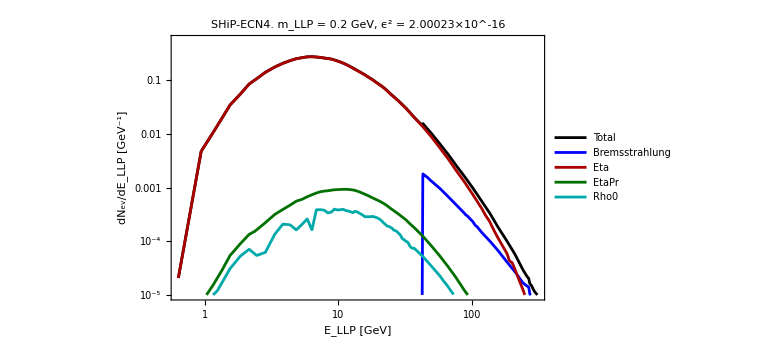

```mathematica
(*Variable = "E_X","z_X","θ_X". The number belongs to the column in the tabulated data*)
iVal:=Association[{"E_LLP" ->2,"θ_LLP"->1,"z_LLP"->3}]
Δxvals["E_LLP"]:=ΔEvals;
Δxvals["z_LLP"]=Δzvals;
Do[Δxvals["θ_X",prod]=Δθvals[prod],{prod,ProductionList}];
LegendX:=Association[{"E_LLP"->"E_LLP [GeV]","θ_LLP"->"θ_LLP [rad]","z_LLP"-> "z_LLP [m]"}]
LegendY:=Association[{"E_LLP"->"dN_ev/dE_LLP [GeV^-1]","θ_LLP"->"dN_ev/dθ_LLP [rad^-1]","z_LLP"-> "dN_ev/dz_LLP [m^-1]"}]
(*Differential number of events*)
NeventsDifferentialDiscretProd[m_,ProdChannel_,coupling_,Variable_]:=Module[{NpotTimesχval},
ival=iVal[Variable];
NpotTimesχval=NpotGivenExperiment*ProbLLP[m,coupling,ProdChannel];
tablegrid0=TableIntegrandDiscret[m,ProdChannel,"True"];
OutGridEfinalTemp=OutGridEnergy[N[m],ProdChannel];
ΔEvals=(Rest[10^OutGridEfinalTemp]-Most[10^OutGridEfinalTemp]);
Δxval=Δxvals[Variable];
cτVal=cτLLP[m,coupling];
brvis=BrVis[m];
ilist=DeleteDuplicates[{ival,1,2,3}];
tablegrid1=SortBy[{#[[ilist[[1]]]],#[[ilist[[2]]]],#[[ilist[[3]]]],#[[4]]}&/@tableGridPrefac[tablegrid0,m,cτVal,0.],{#[[1]],#[[2]],#[[3]]}&];
GridQuantity=tablegrid1[[All,1]]//DeleteDuplicates;
LengthPerVariable=Length[tablegrid1]/Length[GridQuantity];
tab1=NdiffCompiled[tablegrid1,GridQuantity,LengthPerVariable,NpotTimesχval*brvis];
Join[tab1[[All,{1}]],Partition[tab1[[All,2]]*Δxval^-1,1],2]
]
NeventsDifferentialDiscret[m_,coupling_,Variable_]:=Module[{NdiffInt,LegendList,QuantityMinMax,ValueMinMax},
prodlisttemp={};
Do[If[Max[mLLPmin[prod],mminϵ]<m<Min[mLLPmax[prod],mmaxϵ],
prodlisttemp=Join[prodlisttemp,{prod}];
NdiffData[prod]=NeventsDifferentialDiscretProd[m,prod,coupling,Variable];
XvalminmaxNdiff=Select[NdiffData[prod],#[[2]]>10^-40&][[All,1]]//MinMax;
NdiffInt[X_,prod]=If[XvalminmaxNdiff[[1]]<X<XvalminmaxNdiff[[2]],Evaluate[10^Interpolation[{Log10[#[[1]]],Log10[#[[2]]+10^-90]}&/@NdiffData[prod],InterpolationOrder->1][Log10[X]]],0]],{prod,ProductionList}];
NdiffInt[X_,"Total"]=Sum[NdiffInt[X,prod],{prod,prodlisttemp}];
LegendList=Join[{"Total"},prodlisttemp];
QuantityMinMax=Flatten[Table[MinMax[NdiffData[prod][[All,1]]],{prod,prodlisttemp}],1]//MinMax;
ValueMinMax=Max[Max[NdiffData[#][[All,2]]]&/@prodlisttemp];
{Table[NdiffInt[X,prod],{prod,LegendList}],LegendList,QuantityMinMax,ValueMinMax}
]
mvaltest=If[FacilityGivenExperiment=="ESS",0.04,0.2];
couplingvaltest=1.4LowerBoundEstimate[mvaltest,"Eta"];
quantity="E_LLP";
{NdiffTab[X_],LegendList,QuantityMinMax,ValueMinMax}=NeventsDifferentialDiscret[mvaltest,couplingvaltest,quantity];
Do[
prch=LegendList[[i]];
NdiffInt[X_,prch]=NdiffTab[X][[i]];
,{i,1,Length[LegendList]}];
plotdiff=LogLogPlot[Evaluate[Table[NdiffInt[X,prod],{prod,LegendList}]],{X,QuantityMinMax[[1]],QuantityMinMax[[2]]},Frame->True,ImageSize->Large,PlotRange->{All,{10^-5,2ValueMinMax}},PlotStyle->{{Thick,Black},{Thick,Blue},{Thick,Darker@Red},{Thick,Darker@Darker@Green},{Thick,Darker@Cyan},{Thick,Magenta},{Thick,Blue,Dashing[0.02]},{Thick,Darker@Red,Dashing[0.02]},{Thick,Darker@Darker@Green,Dashing[0.02]}},PlotLegends->Placed[Style[#,20]&/@LegendList,Right],FrameLabel->{LegendX[quantity] ,LegendY[quantity]},FrameStyle->Directive[Black, 18],PlotLabel->Style[Row[{SelectedExperiment,". m_LLP = ",mvaltest," GeV, ϵ^2 = ",couplingvaltest//N}],18,Black]]
```

# Exporting tabulated number of events

## Definitions

```mathematica
directory["Nevents"]=FileNameJoin[{NotebookDirectory[],"Tabulated Nevents"}];
directory["Nevents-LLP"]=FileNameJoin[{NotebookDirectory[],"Tabulated Nevents",LLPdirName}];
directory["Nevents-LLP-experiment"]=FileNameJoin[{NotebookDirectory[],"Tabulated Nevents",LLPdirName,SelectedExperiment}];
If[!DirectoryQ[directory[#]],CreateDirectory[directory[#]]]&/@{"Nevents","Nevents-LLP","Nevents-LLP-experiment"};
Print["Filenames with tabulated N_events:"]
Do[FilenameNeventsInt[prod]=ToString@StringForm["Nevents_``_``_at_``_Npot=``.dat",Sequence@@{LLPdirName,prod,SelectedExperiment,NpotGivenExperiment//CForm//ToString}],{prod,ProductionList}]
FilenameNeventsInt[#]&/@ProductionList
Do[mRangeExport[prod]=Join[{0.021,0.026,0.031,0.036,0.041,0.046,0.051,0.056,0.061,0.066,0.07,0.08,0.09,0.1,0.11,0.12,0.125,0.13,0.14,0.15,0.17,0.2,0.215,0.25,0.3,0.35,0.4,0.45,0.5,0.54,0.55,0.6,0.65,0.7,0.72,0.73,0.74,0.75,0.76,0.77,0.775,0.78,0.785,0.79,0.795,0.8,0.81,0.82,0.84,0.9,0.95,0.97,1,1.005,1.01,1.012,1.015,1.017,1.02,1.025,1.03,1.05,1.07,1.09,1.1,1.2,1.3,1.4,1.5,1.6,1.7,1.8,1.9,2.,2.1,2.2,2.3,2.4,2.5,2.6,2.7,2.8,2.9,3.,3.05,3.1,3.2},Table[mLLP,{mLLP,3.21,Max[Table[mLLPmax[prod],{prod,ProductionList}]],(Max[Table[mLLPmax[prod],{prod,ProductionList}]]-3)/10}]]//N
,{prod,ProductionList}];
couplingsRangeExport=Table[10^x,{x,-18.8,-6,0.03}]//N;
```

Filenames with tabulated N_events:

{Nevents_DP_Bremsstrahlung_at_SHiP-ECN4_Npot=6.e20.dat,Nevents_DP_DrellYan_at_SHiP-ECN4_Npot=6.e20.dat,Nevents_DP_Eta_at_SHiP-ECN4_Npot=6.e20.dat,Nevents_DP_EtaPr_at_SHiP-ECN4_Npot=6.e20.dat,Nevents_DP_Pi0_at_SHiP-ECN4_Npot=6.e20.dat,Nevents_DP_Rho0_at_SHiP-ECN4_Npot=6.e20.dat}

## Exporting

## Common definition

```mathematica
BlockExport[ProdChannel_]:=Module[{mlist},
mlist=mRangeExport[ProdChannel];
TabFrom=ParallelTable[Quiet[NeventsDiscret[mlist[[k]],ProdChannel,couplingsRangeExport]],{k,1,Length[mlist],1}];
Export[FileNameJoin[{directory["Nevents-LLP-experiment"],FilenameNeventsInt[ProdChannel]}],Flatten[TabFrom,1],"Table"]
]
Monitor[
Do[
prod=ProductionList[[j]];
BlockExport[prod],{j,1,Length[ProductionList],1}],
Row[{ProgressIndicator[j,{1,Length[ProductionList]}]," Production mode = ",ProductionList[[j]]," (", j,"/",Length[ProductionList],")"}]]//AbsoluteTiming
If[icounter>Length[SelectedExperimentList],BlockEvaluation["Sensitivity"]]
```

{273.999,Null}

# Computing sensitivities

## Basic definitions

```mathematica
LLPdirName="DP";
directory["Sensitivity"]=FileNameJoin[{NotebookDirectory[],"Sensitivity domains"}];
directory["Sensitivity-LLP"]=FileNameJoin[{directory["Sensitivity"],LLPdirName}];
If[!DirectoryQ[directory[#]],CreateDirectory[directory[#]]]&/@{"Sensitivity","Sensitivity-LLP"};
directory["Nevents-LLP"]=FileNameJoin[{NotebookDirectory[],"Tabulated Nevents",LLPdirName}];
dropdownDialog[list_,phrase_]:=DialogInput[{choice=""},Column[{TextCell[phrase],PopupMenu[Dynamic[choice],list],Button["OK",DialogReturn[choice]]}]]
infoDialog[phrase_]:=DialogInput[{choice=""},Column[{TextCell[phrase],Button["Proceed",DialogReturn[choice]]}]]
selectionDialog[list_,phrase_]:=DialogInput[{choice={}},Column[{Row[{phrase}],Pane[TogglerBar[Dynamic[choice],list,Appearance->"Vertical"->{Automatic,5}],ImageSize->{Automatic,Automatic},Scrollbars->{False,True}],Button["OK",DialogReturn[choice]]}]]
ExperimentDirectoriesListNevents=Select[FileNames["*",directory["Nevents-LLP"],1],DirectoryQ];
Print["List of available experiments with tabulated N_events for " <>LLPdirName<>":"]
ExperimentsListNevents=Table[FileNameTake[ExperimentDirectoriesListNevents[[i]],-1],{i,1,Length[ExperimentDirectoriesListNevents],1}]//Sort;
ExperimentsListNevents//TableForm
If[Length[ExperimentsListNevents]==0,Print["No experiment is available, generate first the acceptance for the given experiment using module 1"],
SelectedExperimentList=If[Length[ExperimentsListNevents]≠0,selectionDialog[ExperimentsListNevents,"Select the experiments for which the sensitivity will be computed:"]];
icounter=1;
BlockEvaluation[tag_]:=Block[{},
nb=EvaluationNotebook[];
NotebookFind[nb,tag,All,CellTags];
SelectionEvaluate[nb]
];
Do[
BlockEvaluation["Sensitivity-computation"];
,{icounter,1,Length[SelectedExperimentList],1}]
]
```

List of available experiments with tabulated N_events for DP:

SHiP-ECN4

## Specifying the experiment and interpolating tabulated number of events

## Selecting the experiment

```mathematica
Print["Selected experiment:"]
GivenExperimentForSensitivityComputation=SelectedExperimentList[[icounter++]]
CondANUBIS=MemberQ[{"ANUBIS-shaft-volume-1","ANUBIS-shaft-volume-2","ANUBIS-shaft-volume-3"},GivenExperimentForSensitivityComputation];
If[CondANUBIS==True,infoDialog[Row[{"One of the modules of ANUBIS-shaft is chosen. The full sensitivity includes three modules. The importing will be over all modules, so for all ot the the sensitivity has to be computed"}]]]
If[CondANUBIS==False,GivenExperimentForSensitivityComputationList={GivenExperimentForSensitivityComputation},GivenExperimentForSensitivityComputationList={"ANUBIS-shaft-volume-1","ANUBIS-shaft-volume-2","ANUBIS-shaft-volume-3"}];
PathsNeventsSelected={};
Do[PathsNeventsSelected=Join[PathsNeventsSelected,FileNames["*.dat",FileNameJoin[{directory["Nevents-LLP"],exp}]]],{exp,GivenExperimentForSensitivityComputationList}];
(*Creating the directory for exporting sensitivity curves*)
ExperimentFolder=If[CondANUBIS==True,"ANUBIS",GivenExperimentForSensitivityComputation];
directory["Sensitivity-LLP-exp"]=FileNameJoin[{directory["Sensitivity-LLP"],ExperimentFolder}];
If[!DirectoryQ[directory["Sensitivity-LLP-exp"]],CreateDirectory[directory["Sensitivity-LLP-exp"]]]
```

Selected experiment:

SHiP-ECN4

## Importing data and interpolations

List of production channels:

Mother | Experiment | N_PoT
Bremsstrahlung | SHiP-ECN4 | 6.e20
DrellYan | SHiP-ECN4 | 6.e20
Eta | SHiP-ECN4 | 6.e20
EtaPr | SHiP-ECN4 | 6.e20
Pi0 | SHiP-ECN4 | 6.e20
Rho0 | SHiP-ECN4 | 6.e20

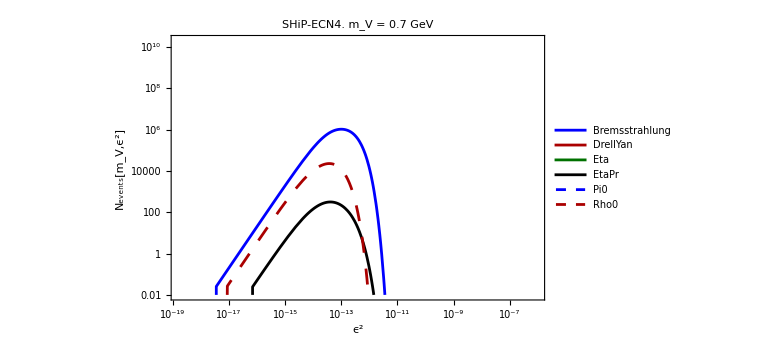

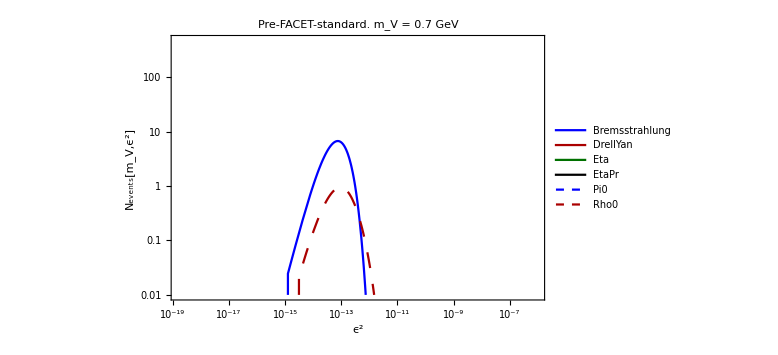

```mathematica
(*______________________________________________________*)
(*Importing and interpolation*)
(*______________________________________________________*)
Print["List of production channels:"]
FilenamesNeventsSelected=Table[Last@FileNameSplit@PathsNeventsSelected[[i]],{i,1,Length[PathsNeventsSelected],1}];
FilenameParameters[i_]:=StringCases[FilenamesNeventsSelected[[i]],"Nevents_"<>LLPdirName<>"_"~~mother__~~"_at_"~~experiment__~~"_Npot="~~Npot__~~".dat":>{mother,experiment,Npot}][[1]]
ProductionInfoList=Table[FilenameParameters[i],{i,1,Length[FilenamesNeventsSelected],1}];
Join[{{"Mother","Experiment","N_PoT"}},ProductionInfoList]//TableForm
ProductionChannelsList=ProductionInfoList[[All,1]];
NpotDefault=Interpreter["Number"][ProductionInfoList[[1]][[3]]];
NeventsTabulated//Clear;
ϵreco[mLLP_]=1;
If[StringContainsQ[GivenExperimentForSensitivityComputation,"LHCb-downstream"],
ϵreco[mLLP_]=0.4];
If[StringContainsQ[GivenExperimentForSensitivityComputation,"NuCal"],
ϵreco[mLLP_]=0.7];
If[StringContainsQ[GivenExperimentForSensitivityComputation,"CHARM"],
ϵreco[mLLP_]=0.6];
Do[
Module[{prod},
prod=ProductionChannelsList[[i]];
(*The condition if one sums the number of events for the same production mode over several experiments*)
IfprodExists=MemberQ[Keys[DownValues@NeventsTabulated][[All,1,1]],prod];
NeventsTabulated[prod]=If[!IfprodExists,Import[PathsNeventsSelected[[i]],"Table"],Join[NeventsTabulated[prod][[All,{1,2}]],NeventsTabulated[prod][[All,{3}]]+Import[PathsNeventsSelected[[i]],"Table"][[All,{3}]]]];
{mminmax[prod],couplingminmax[prod]}=(NeventsTabulated[prod][[All,#]]//MinMax)&/@{1,2};
NevMax[prod]=NeventsTabulated[prod][[All,3]]//Max;
NevInt[mLLP_,ϵ2_,prod]=ϵreco[mLLP]*If[mminmax[prod][[1]]≤ mLLP≤mminmax[prod][[2]]&&couplingminmax[prod][[1]]≤ϵ2≤couplingminmax[prod][[2]],Evaluate[10^(Interpolation[{Log10[#[[1]]],Log10[#[[2]]],Log10[#[[3]]+10^-90]}&/@NeventsTabulated[prod],InterpolationOrder->1][Log10[mLLP],Log10[ϵ2]])],0];
]
,{i,1,Length[ProductionInfoList],1}]
{mminmaxOverall,couplingminmaxOverall}=MinMax[Table[#[prod],{prod,ProductionChannelsList}]//Flatten]&/@{mminmax,couplingminmax};
NevMaxOverall=Max[Table[NevMax[prod],{prod,ProductionChannelsList}]];
NevIntOverall[mLLP_,ϵ2_]=Sum[NevInt[mLLP,ϵ2,prod],{prod,ProductionChannelsList}];
pt[mLLP_]:=LogLogPlot[Evaluate[Table[NevInt[mLLP,y,prod],{prod,ProductionChannelsList}]],{y,couplingminmaxOverall[[1]],couplingminmaxOverall[[2]]},PlotLegends->Placed[Style[#,15]&/@ProductionChannelsList,Right],PlotRange->{couplingminmaxOverall,{10^-2,NevMaxOverall}},Frame->True,ImageSize->Large,FrameLabel->{"ϵ^2" , "N_events[m_V,ϵ^2]"},FrameStyle->Directive[Black, 23],PlotStyle->{{Thick,Blue},{Thick,Darker@Red},{Thick,Darker@Darker@Green},{Thick,Black},{Thick,Blue,Dashing[0.02]},{Thick,Darker@Red,Dashing[0.02]},{Thick,Darker@Darker@Green,Dashing[0.02]},{Thick,Black,Dashing[0.02]}},PlotLabel->Style[Row[{ExperimentFolder,". m_V = ",mLLP, " GeV"}],20,Black]]
pt[0.7]
```

## Sensitivity

## Events density plot

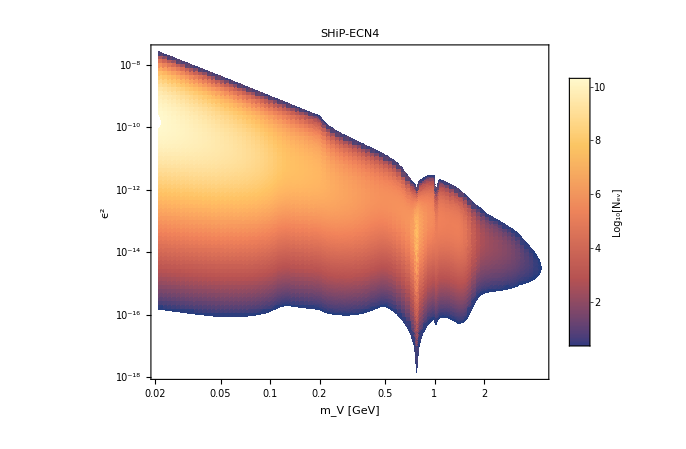

/Users/alberto/SensCalc/plots/SensCalc/NeventsDensityPlotExample.pdf

```mathematica
plot=DensityPlot[Evaluate[Log10[NevIntOverall[mLLP,ϵ2]]],{mLLP,mminmaxOverall[[1]],mminmaxOverall[[2]]},{ϵ2,couplingminmaxOverall[[1]],couplingminmaxOverall[[2]]},ScalingFunctions->{"Log","Log"},AspectRatio->0.78,PlotRange->{All,All,{Log10[2.3],Log10[NevMaxOverall]}},ImageSize->Large,FrameLabel->{"m_V [GeV]","ϵ^2"}, Frame-> True, FrameStyle->Directive[Black, 25],PlotPoints->100,PlotLegends->Placed[BarLegend[{Automatic,{Log10[2.3],Log10[NevMaxOverall]}},LegendMarkerSize->340,LegendLabel->Placed["Log_10[N_ev]",Bottom],LabelStyle->{FontSize->22},Method->{FrameStyle->Black,AxesStyle->None,TicksStyle->Black}],Right],PlotLabel->Style[Row[{ExperimentFolder}],20,Black](*,FrameTicks->{{Automatic,Automatic},{TicksPlotx,None}}*)]
Export[FileNameJoin[{NotebookDirectory[],"plots/SensCalc/NeventsDensityPlotExample.pdf"}],plot,"AllowRasterization"->False]
```

## Importing constraints

```mathematica
importformat["txt"]=importformat["dat"]="Table";
importformat["m"]=importformat["mx"]="MX";
importformat["xls"]="XLS";
dir=FileNameJoin[{NotebookDirectory[],"contours",LLPdirName}];
If[DirectoryQ[dir],
filenames=FileNames[LLPdirName<>"-excluded*",dir,Infinity];
ExcludedRegions[LLPdirName]=Import[#,importformat[FileExtension[#]]]&/@FileNames[LLPdirName<>"-excluded*",dir,Infinity];
];
If[!DirectoryQ[dir],
ExcludedRegions[LLPdirName]={{{10.,10.}}};
]
```

## Sensitivity evaluation

N_PoT for computation | N_(ev, min) | Selected production modes
6.×10^20 | 2.3 | Bremsstrahlung
DrellYan
Eta
EtaPr
Pi0
Rho0

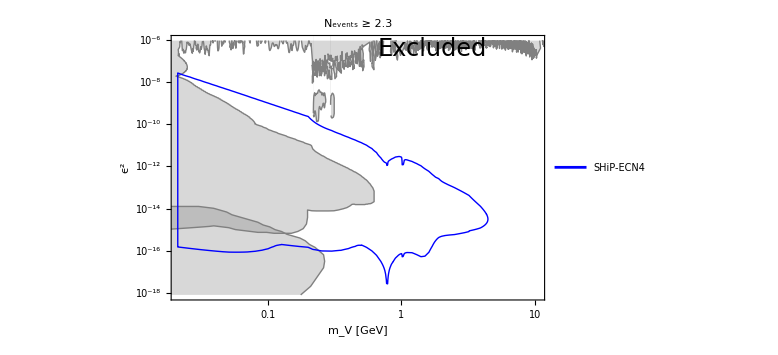

```mathematica
SensitivityBlock[Nev_,Npot_,SelectedProduction_]:=Block[{},
NevTot[mLLP_,ϵ2_]=Sum[NevInt[mLLP,ϵ2,prod],{prod,SelectedProduction}];
RegSens=RegionPlot[Npot/NpotDefault NevTot[10^mLLP,10^ϵ2]≥Nev,{mLLP,Log10[mminmaxOverall[[1]]],Log10[mminmaxOverall[[2]]]},{ϵ2,Log10[couplingminmaxOverall[[1]]],Log10[couplingminmaxOverall[[2]]]},PlotPoints->200];
SensTemp=Cases[Normal@RegSens,Line[x_]:>x,Infinity];
Sens=Table[{10^#[[1]],10^#[[2]]}&/@SensTemp[[i]],{i,1,Length[SensTemp],1}];
Export[FileNameJoin[{directory["Sensitivity-LLP-exp"],ToString@StringForm["Sensitivity_``_at_``_Nev=``_Npot=``.xls",Sequence@@{LLPdirName,ExperimentFolder,Nev//ToString,Npot//CForm//ToString}]}],Sens];
Sens
]
productionlist=Join[{"All"},ProductionChannelsList];
DynamicModule[{input1=NpotDefault,input2=2.3,choice={"All"},list,phrase},
DialogInput[Column[{Style[ExperimentFolder,Bold],TextCell["Enter the number of proton collisions:"],InputField[Dynamic[input1],Expression],TextCell["Enter the value of N_ev,min for which the sensitivity will be computed:"],InputField[Dynamic[input2],Expression],Row[{"Select the production channels to be used for the sensitivity calculation:"}],Pane[TogglerBar[Dynamic[choice],productionlist,Appearance->"Vertical"->{Automatic,1}],ImageSize->{Automatic,Automatic},Scrollbars->{False,True}],Button["Submit",DialogReturn[{NpotVal,NevMinVal,SelectedProduction}={input1,input2,choice}//N],ImageSize->Automatic]}]]];
If[MemberQ[SelectedProduction,"All"],SelectedProduction=ProductionChannelsList;]
{{"N_PoT for computation","N_(ev, min)","Selected production modes"},{NpotVal,NevMinVal,SelectedProduction}}//TableForm
sens=SensitivityBlock[NevMinVal,NpotVal,SelectedProduction];
Show[ListLogLogPlot[Cases[ExcludedRegions[LLPdirName],_?MatrixQ,All],Joined->{True,True,True,True},Frame-> True,FrameLabel->{"m_V [GeV]" , "ϵ^2"},FrameStyle->Directive[Black, 23],PlotStyle->{{Thick,Gray}},Filling->{1->{True,Directive[Gray,Opacity[0.3]]},2->{True,Directive[Gray,Opacity[0.3]]},3->{True,Directive[Gray,Opacity[0.3]]},4->{True,Directive[Gray,Opacity[0.3]]}},ImageSize->Large,PlotRange->{{1.01mminmaxOverall[[1]],1.1mminmaxOverall[[2]]},{0.3Min[Flatten[Sens]],0.99couplingminmaxOverall[[2]]}},PlotLabel->Style[Row[{"N_events ≥ ",NevMinVal}],18,Black]],
ListLogLogPlot[Cases[sens,_?MatrixQ,All],Joined->{True,True,True,True},PlotStyle->Flatten[{ConstantArray[{Thick,Blue},If[MatrixQ[sens],1,Length@sens]]},1],ImageSize->Large,PlotRange->{{1.01mminmaxOverall[[1]],1.1mminmaxOverall[[2]]},{couplingminmaxOverall[[1]],Max[0.2,0.99couplingminmaxOverall[[2]]]}},PlotLabel->Style[Row[{"N_events ≥ ",NevMinVal}],18,Black],PlotLegends->Placed[Style[#,15]&/@{GivenExperimentForSensitivityComputation},{0.2,0.15}]],Graphics[{Text[Style["Excluded",24,Black],Scaled[{0.7,0.95}]]}]]
```

# Deleting generated cells

```mathematica
FrontEndTokenExecute["DeleteGeneratedCells"];
FrontEndTokenExecute["SelectAll"];
FrontEndTokenExecute["SelectionCloseAllGroups"];
```